# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=256*numClasses;
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize,RandomUniformSoftBits[#]&,RandomUniformSoftBits[#]&],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

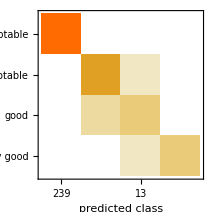
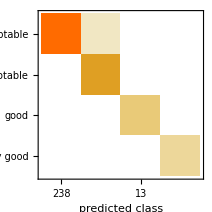
{Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.80.6) %
Accuracy baseline | (69.12.5) %
Geometric mean of probabilities | 0.971 ± 0.0093
Mean cross entropy | 0.0292 ± 0.0096
Single evaluation time | 5.88 ms/example
Batch evaluation speed | 990. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.710.29) %
Accuracy baseline | (69.12.5) %
Geometric mean of probabilities | 0.979 ± 0.0092
Mean cross entropy | 0.0214 ± 0.0094
Single evaluation time | 5.76 ms/example
Batch evaluation speed | 2.09 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
eval=HardNetClassifyEvaluation[hncwt]
```

<|Accuracy→0.991329,Results→<|<|Prediction→unacceptable,Target→unacceptable|>→236,<|Prediction→acceptable,Target→acceptable|>→82,<|Prediction→good,Target→good|>→13,<|Prediction→very good,Target→very good|>→12,<|Prediction→acceptable,Target→unacceptable|>→3|>|>

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2]
```

<|Accuracy→0.991329,Results→<|<|Prediction→unacceptable,Target→unacceptable|>→236,<|Prediction→acceptable,Target→acceptable|>→82,<|Prediction→good,Target→good|>→13,<|Prediction→very good,Target→very good|>→12,<|Prediction→acceptable,Target→unacceptable|>→3|>|>

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

5.5 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Acceptability",Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

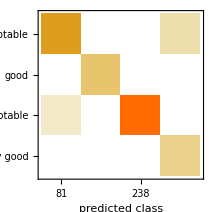
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 346
Accuracy | (99.10.5) %
Accuracy baseline | (69.12.5) %
Geometric mean of probabilities | 0.956 ± 0.03
Mean cross entropy | 0.0445 ± 0.032
Single evaluation time | 7.04 ms/example
Batch evaluation speed | 1.43 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Acceptability"]
```

```mathematica
Information[classifier,"FunctionMemory"]
```

753. kB

## Notes

```mathematica
softWeights=Flatten[ExtractWeights[trainedSoftNet]];
```

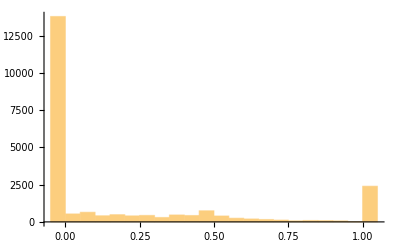

```mathematica
Histogram[softWeights,PlotRange->All]
```